```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/dispersion-relation

```mathematica
Get["../../neupackage/mma/dispersion-relation.wl"]
```

## Solving Multiangle Problem

Using beams
In Unit of omega_v

```mathematica
nBeams=4;
angleRange={Pi/3,5Pi/6};
```

Devided the angle range into [nBeams] beams

```mathematica
dividerRS=(1/Sin[#1]-1/Sin[#2])&[First@angleRange,Last@angleRange]/(nBeams-1)

(* dividerRS does NOT work *)

dividerA=(#1-#2)&[First@angleRange,Last@angleRange]/(nBeams-1)
```

1/3 (-2+2/(√3))

-π/6

Define a function to find the corresponding angles of the nth beam

```mathematica
beamAngleRS[nth_]:=ArcSin@(1/(1/Sin[#1]-(nth-1)dividerRS))&[First@angleRange]
(* beamAngleRS does NOT work *)

beamAngleA[nth_]:=(#1-(nth-1)dividerA)&[First@angleRange]
```

```mathematica
(* Test the consistancy of definitions *)
{Sin@#1,Sin@#2}&[First@angleRange,Last@angleRange]

{#,Sin@#}&[beamAngleRS[1]]
{#,Sin@#}&[beamAngleRS[nBeams]]


{#,Sin@#}&[beamAngleA[1]]
{#,Sin@#}&[beamAngleA[nBeams]]
```

{(√3)/2,1/2}

{π/3,(√3)/2}

{π/6,1/2}

{π/3,(√3)/2}

{(5 π)/6,1/2}

```mathematica
Table[{#,Sin@#}&[beamAngleA[i]],{i,1,10}]
```

{{π/3,(√3)/2},{π/2,1},{(2 π)/3,(√3)/2},{(5 π)/6,1/2},{π,0},{(7 π)/6,-1/2},{(4 π)/3,-(√3)/2},{(3 π)/2,-1},{(5 π)/3,-(√3)/2},{(11 π)/6,-1/2}}

Generate etaHierarchys which is determined by hierarchy and also neutrino or antineutrino

```mathematica
(* All neutrinos *)
etaHierarchy=Table[1,{i,1,nBeams}]

(* Using energy scale unit omegav so omegav is 1 *)
omegav=Table[1,{i,1,nBeams}]

(* neutrino self interaction *)
muList = Join[
Table[1,{i,1,nBeams/2}],
Table[-1,{i,1,nBeams/2}]
]

(* Matter is in unit of omegav *)

lambda = 4Pi/nBeams
```

{1,1,1,1}

{1,1,1,1}

{1,1,-1,-1}

π

## Raffelt’s Approach

```mathematica
pltDiffBeams[beams_]:=dataPltNBeamsPlt[
Join[Table[1/beams,{n,1,beams/2}],Table[-1/beams,{n,1,beams/2}]],
Table[beamAngleA[n],{n,0,beams-1}],{-10,10},0.049,{{-10,10},{-10,10}}]
```

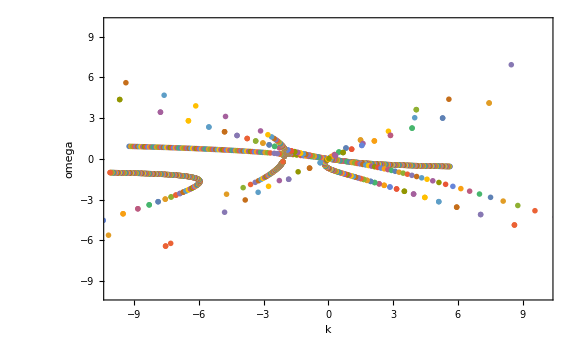

```mathematica
pltDiffBeams[nBeams]
```

## The Standard Approach

The Matrix

```mathematica
n1Mat=N@DiagonalMatrix[
Table[-kz Sin@beamAngleA[n]-kx Cos@beamAngleA[n]-1/2 (lambda-etaHierarchy[[n]] omegav[[n]]),{n,1,nBeams}]
];

%//MatrixForm
```

(-1.0708-0.5 kx-0.866025 kz | 0. | 0. | 0.
0. | -1.0708-1. kz | 0. | 0.
0. | 0. | -1.0708+0.5 kx-0.866025 kz | 0.
0. | 0. | 0. | -1.0708+0.866025 kx-0.5 kz)

```mathematica
n2Mat=1/2N@DiagonalMatrix[
Table[
Total@Table[muList[[j]](1-Cos@(beamAngleA[i]-beamAngleA[j])),{j,1,nBeams}],
{i,1,nBeams}]
];
%//MatrixForm
```

(-0.683013 | 0. | 0. | 0.
0. | -0.25 | 0. | 0.
0. | 0. | 0.25 | 0.
0. | 0. | 0. | 0.683013)

```mathematica
mMat=1/2N@Table[
muList[[j]](1-Cos@(beamAngleA[i]-beamAngleA[j])),
{i,1,nBeams},{j,1,nBeams}];
%//MatrixForm
```

(0. | 0.0669873 | -0.25 | -0.5
0.0669873 | 0. | -0.0669873 | -0.25
0.25 | 0.0669873 | 0. | -0.0669873
0.5 | 0.25 | -0.0669873 | 0.)

Calcualte Using Eigenvalues

```mathematica
detFun[kx_,kz_]=Eigenvalues[n1Mat+n2Mat+mMat]
```

{Root[5.12732-10.0115 kx+1.7831 kx^2+1.3208 kx^3+15.3942 kz-20.6237 kx kz+0.655689 kx^2 kz+1. kx^3 kz+17.2362 kz^2-13.9584 kx kz^2-0.57735 kx^2 kz^2+8.78022 kz^3-3. kx kz^3+1.73205 kz^4+(21.1157-23.8587 kx-0.106873 kx^2+1. kx^3+47.18 kz-31.5999 kx kz-1.73205 kx^2 kz+35.6976 kz^2-9.9282 kx kz^2+9.19615 kz^3) #1+(31.0436-17.7363 kx-1.1547 kx^2+46.6458 kz-10.9282 kx kz+17.7735 kz^2) #1^2+(19.7832-4. kx+14.9282 kz) #1^3+4.6188 #1^4&,1],Root[5.12732-10.0115 kx+1.7831 kx^2+1.3208 kx^3+15.3942 kz-20.6237 kx kz+0.655689 kx^2 kz+1. kx^3 kz+17.2362 kz^2-13.9584 kx kz^2-0.57735 kx^2 kz^2+8.78022 kz^3-3. kx kz^3+1.73205 kz^4+(21.1157-23.8587 kx-0.106873 kx^2+1. kx^3+47.18 kz-31.5999 kx kz-1.73205 kx^2 kz+35.6976 kz^2-9.9282 kx kz^2+9.19615 kz^3) #1+(31.0436-17.7363 kx-1.1547 kx^2+46.6458 kz-10.9282 kx kz+17.7735 kz^2) #1^2+(19.7832-4. kx+14.9282 kz) #1^3+4.6188 #1^4&,2],Root[5.12732-10.0115 kx+1.7831 kx^2+1.3208 kx^3+15.3942 kz-20.6237 kx kz+0.655689 kx^2 kz+1. kx^3 kz+17.2362 kz^2-13.9584 kx kz^2-0.57735 kx^2 kz^2+8.78022 kz^3-3. kx kz^3+1.73205 kz^4+(21.1157-23.8587 kx-0.106873 kx^2+1. kx^3+47.18 kz-31.5999 kx kz-1.73205 kx^2 kz+35.6976 kz^2-9.9282 kx kz^2+9.19615 kz^3) #1+(31.0436-17.7363 kx-1.1547 kx^2+46.6458 kz-10.9282 kx kz+17.7735 kz^2) #1^2+(19.7832-4. kx+14.9282 kz) #1^3+4.6188 #1^4&,3],Root[5.12732-10.0115 kx+1.7831 kx^2+1.3208 kx^3+15.3942 kz-20.6237 kx kz+0.655689 kx^2 kz+1. kx^3 kz+17.2362 kz^2-13.9584 kx kz^2-0.57735 kx^2 kz^2+8.78022 kz^3-3. kx kz^3+1.73205 kz^4+(21.1157-23.8587 kx-0.106873 kx^2+1. kx^3+47.18 kz-31.5999 kx kz-1.73205 kx^2 kz+35.6976 kz^2-9.9282 kx kz^2+9.19615 kz^3) #1+(31.0436-17.7363 kx-1.1547 kx^2+46.6458 kz-10.9282 kx kz+17.7735 kz^2) #1^2+(19.7832-4. kx+14.9282 kz) #1^3+4.6188 #1^4&,4]}

```mathematica
dataPlt=Table[
Table[{kz,detFun[0,kz][[i]]},{kz,-20,10,0.5}],
{i,1,nBeams}];
```

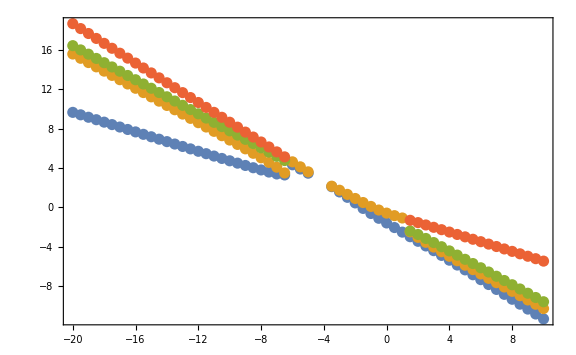

```mathematica
ListPlot[dataPlt,Frame->True,ImageSize->Large,Axes->False]
```

```mathematica
Export["export/multiangle-beams-example1-data.csv",dataPlt]
```

export/multiangle-beams-example1-data.csv

Calculate Using Determinant

The determine

```mathematica
detFun[omegat_,kx_,kz_]=Det[n1Mat+n2Mat+mMat]
```

1.1101-2.16756 kx+0.386053 kx^2+0.285961 kx^3+3.33293 kz-4.46517 kx kz+0.141961 kx^2 kz+0.216506 kx^3 kz+3.73175 kz^2-3.02209 kx kz^2-0.125 kx^2 kz^2+1.90097 kz^3-0.649519 kx kz^3+0.375 kz^4

Assuming kz = nref omega
and fix kx

```mathematica
detFun[omegat,0,nref omegat]
```

1.1101+3.33293 nref omegat+3.73175 nref^2 omegat^2+1.90097 nref^3 omegat^3+0.375 nref^4 omegat^4

```mathematica
sol[nref_]=omegat/.Solve[detFun[omegat,0,nref omegat]==0,omegat,Reals];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
data2Plt[nref_]:=Transpose@{sol[nref],nref sol[nref]};
```

```mathematica
Flatten[{{{1,2},{3,4}},{{5,6},{7,8}}},1]
```

{{1,2},{3,4},{5,6},{7,8}}

```mathematica
dataClean=Flatten[
Table[data2Plt[nref],{nref,-10,10,0.02}]
,1];
```

Root::deg: 8.90528×10^44 has fewer than 1 root(s) as a polynomial in #1.

Root::deg: 8.90528×10^44 has fewer than 2 root(s) as a polynomial in #1.

Root::deg: 8.90528×10^44 has fewer than 1 root(s) as a polynomial in #1.

General::stop: Further output of Root :: deg will be suppressed during this calculation.

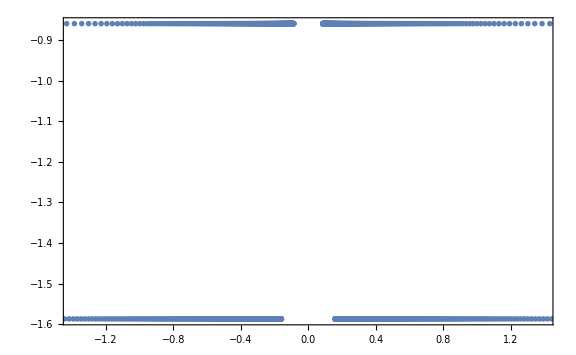

```mathematica
ListPlot[dataClean,Frame->True,ImageSize->Large,Axes->False]
```

```mathematica
Export["export/multiangle-beams-example1-data.csv",dataClean]
```

export/multiangle-beams-example1-data.csv

## Work out the Continuous Results

To verify this result, I should plot the continuous case.

## Tests

```mathematica
Table[
Table[
"i="<>ToString@i<>"; j="<>ToString@j,
{i,1,nBeams}],
{j,1,nBeams}];
%//MatrixForm
```

(i=1; j=1 | i=2; j=1 | i=3; j=1 | i=4; j=1 | i=5; j=1 | i=6; j=1 | i=7; j=1 | i=8; j=1 | i=9; j=1 | i=10; j=1
i=1; j=2 | i=2; j=2 | i=3; j=2 | i=4; j=2 | i=5; j=2 | i=6; j=2 | i=7; j=2 | i=8; j=2 | i=9; j=2 | i=10; j=2
i=1; j=3 | i=2; j=3 | i=3; j=3 | i=4; j=3 | i=5; j=3 | i=6; j=3 | i=7; j=3 | i=8; j=3 | i=9; j=3 | i=10; j=3
i=1; j=4 | i=2; j=4 | i=3; j=4 | i=4; j=4 | i=5; j=4 | i=6; j=4 | i=7; j=4 | i=8; j=4 | i=9; j=4 | i=10; j=4
i=1; j=5 | i=2; j=5 | i=3; j=5 | i=4; j=5 | i=5; j=5 | i=6; j=5 | i=7; j=5 | i=8; j=5 | i=9; j=5 | i=10; j=5
i=1; j=6 | i=2; j=6 | i=3; j=6 | i=4; j=6 | i=5; j=6 | i=6; j=6 | i=7; j=6 | i=8; j=6 | i=9; j=6 | i=10; j=6
i=1; j=7 | i=2; j=7 | i=3; j=7 | i=4; j=7 | i=5; j=7 | i=6; j=7 | i=7; j=7 | i=8; j=7 | i=9; j=7 | i=10; j=7
i=1; j=8 | i=2; j=8 | i=3; j=8 | i=4; j=8 | i=5; j=8 | i=6; j=8 | i=7; j=8 | i=8; j=8 | i=9; j=8 | i=10; j=8
i=1; j=9 | i=2; j=9 | i=3; j=9 | i=4; j=9 | i=5; j=9 | i=6; j=9 | i=7; j=9 | i=8; j=9 | i=9; j=9 | i=10; j=9
i=1; j=10 | i=2; j=10 | i=3; j=10 | i=4; j=10 | i=5; j=10 | i=6; j=10 | i=7; j=10 | i=8; j=10 | i=9; j=10 | i=10; j=10)